# 波的衍射和干涉

### 单缝衍射

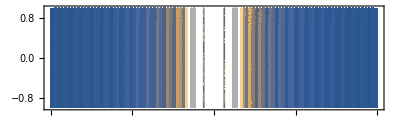

```mathematica
DensityPlot[Sin[u]^2/u^2,{u,-50,50},{y,-1,1},PlotPoints->100,AspectRatio->0.3]
```

### 单孔衍射

```mathematica
DensityPlot[Sin[u]^2/u^2,{u,-50,50},{y,-1,1},PlotPoints->100,AspectRatio->0.3]
```

```mathematica
Plot3D[Sin[5Norm[{x,y}]],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u,v,Sin[5Norm[{u,v}]]},{u,-3,3},{v,-3,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{r Cos[θ],r Sin[θ],0.5 Sin[5r]},{θ,-π,π},{r,0,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{r Cos[θ],r Sin[θ],0.5 Sin[5r]}+{1,1,0},{r Cos[θ],r Sin[θ],0.5 Sin[5r]}+{-1,-1,0}},{θ,-π,π},{r,0,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{r Cos[θ],r Sin[θ],0.5 Sin[5r]}+{1,1,0},{r Cos[θ],r Sin[θ],0.5 Sin[5r]}+{-1,-1,0}},{θ,-π,π},{r,0,3}]
```

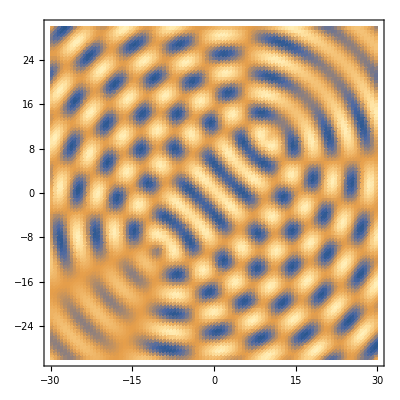

```mathematica
DensityPlot[0.1Sin[Norm[{x,y}-{10,10}]]+0.1Sin[Norm[{x,y}-{-10,-10}]-1],{x,-30,30},{y,-30,30},PlotPoints->100]
```